# Profile Analysis

```mathematica
ClearAll["Global`*"]
```

## Check algorithm

Use one benchmark point from cosmoTransitions, check whether can produce correct bounce action by reading profile data and compute here.

```mathematica
DumpGet[NotebookDirectory[]<>"/output/highT.m"]
```

```mathematica
Vpotential[h_,S_]=VhighT2d[5,0.245,h,S,18.08448948742459];
```

```mathematica
FindMinimum[Vpotential[h,S],{h,S}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.08092×10^8,{h→94.0961,S→-404.376}}

```mathematica
Rdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,1]];
hdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,2]];
Sdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,3]];
```

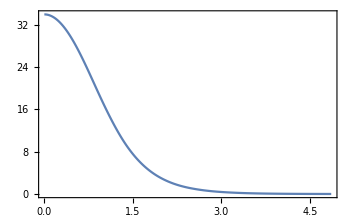

```mathematica
ListLinePlot[{Transpose[{Rdata,hdata}]}]
```

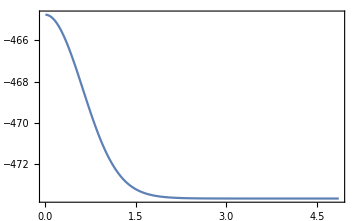

```mathematica
ListLinePlot[Transpose[{Rdata,Sdata}]]
```

```mathematica
hprofile[r_]:=Interpolation[Transpose[{Rdata,hdata}]][r]
Sprofile[r_]:=Interpolation[Transpose[{Rdata,Sdata}]][r]
```

```mathematica
Min[hdata]
```

0.014221

```mathematica
Kinh[r_]=1/2 hprofile'[r]^2;
KinS[r_]=1/2 Sprofile'[r]^2;
potential[r_]:=Vpotential[hprofile[r],Sprofile[r]]-Vpotential[Min[hdata],Min[Sdata]]
```

```mathematica
4π NIntegrate[r^2(Kinh[r]+KinS[r]+potential[r]),{r,0,Max[Rdata]}](*2d action*)
4π NIntegrate[r^2(Kinh[r]+potential[r]),{r,0,Max[Rdata]}](*1d action*)
```

2740.54

2538.59

The error between this and python is very small. So the computation method is correct.

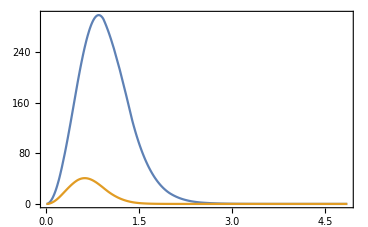

```mathematica
Plot[{Kinh[r],KinS[r]},{r,0,Max[Rdata]},PlotRange->Full]
```

```mathematica
A=15.08095388751636;
μS=31.037748419021955;
Ratio[r_]=(A/μS^2 hprofile[r])^2;(*Analytical solution of the ratio*)
```

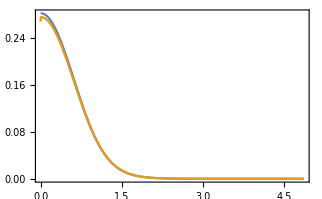

```mathematica
Plot[{Ratio[r],KinS[r]/Kinh[r]},{r,0,Max[Rdata]}]
```

This shows that the prediction is correct. The ratio between the kinetic energy from the bounce solution agrees with our prediction.

## Show comparison

```mathematica
ClearAll["Global`*"]
```

```mathematica
mh=125.13;
v=174.;
μH2[mS_,sinθ_]:=1/2(mh^2(1-sinθ^2)+mS^2 sinθ^2);
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mh^2-mS^2)sinθ √(1-sinθ^2))/(√2 v);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
sin[mS_]:=√(19 mS^2/(mh^2-mS^2))(*Set the fine-tuning to be 5%*)
```

```mathematica
mSlist=Join[Table[mS,{mS,0.5,2,1.5/9}],Table[mS,{mS,2.1,10,7.9/19}]]
```

{0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667,1.83333,2.,2.1,2.51579,2.93158,3.34737,3.76316,4.17895,4.59474,5.01053,5.42632,5.84211,6.25789,6.67368,7.08947,7.50526,7.92105,8.33684,8.75263,9.16842,9.58421,10.}

```mathematica
Files=FileNames["*.csv",NotebookDirectory[]<>"output/profile"];
For[i=1,i<=Length[Files],i++,
datalist[i]=Import[Files[[i]]];
Rlist[i]=datalist[i][[All,1]];
Hlist[i]=datalist[i][[All,2]];
Slist[i]=datalist[i][[All,3]]
]
```

```mathematica
Hfunclist=Table[Interpolation[Transpose[{Rlist[i],Hlist[i]}]],{i,1,30}];
Sfunclist=Table[Interpolation[Transpose[{Rlist[i],Slist[i]}]],{i,1,30}];
```

```mathematica
For[j=1,j<=Length[Files],j++,
Kinh[s_]:=1/2 D[Hfunclist[[j]][r],r]^2/.{r->s};
KinS[s_]:=1/2 D[Sfunclist[[j]][r],r]^2/.{r->s};
Kinhinte[j]=4π NIntegrate[r^2 Kinh[r],{r,0,Max[Rlist[j]]}];
KinSinte[j]=4π NIntegrate[r^2 KinS[r],{r,0,Max[Rlist[j]]}];
Ratio[j]=KinSinte[j]/Kinhinte[j]
]
```

```mathematica
Ratiolist=Table[Ratio[i],{i,Length[Files]}]
```

{5.12828,3.1428,2.17509,0.0306277,1.62237,1.26999,1.02746,0.852555,0.721788,0.620554,0.540865,0.500602,0.375621,0.293571,0.236291,0.194081,0.162399,0.137812,0.118956,0.103008,0.0899209,0.0790634,0.0699572,0.0622363,0.0556392,0.0499531,0.0450273,0.0406684,0.0369069,0.033574}

There is an extraordinary data point. No idea why that happens. But other looks reasonable. Drop it.

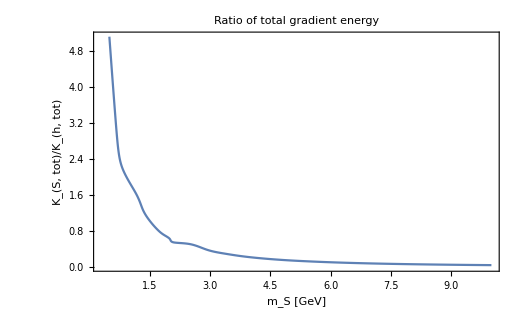

```mathematica
ListLinePlot[Transpose[{Drop[mSlist,{4}],Drop[Ratiolist,{4}]}],PlotRange->Full,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["K_(S, tot)/K_(h, tot)",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotLabel->Style["Ratio of total gradient energy"],ImageSize->520,InterpolationOrder->3]
```

### Plot out the energy profile

```mathematica
Hfunc1[r_]:=Interpolation[Transpose[{Rlist[8],Hlist[8]}]][r];
Sfunc1[r_]:=Interpolation[Transpose[{Rlist[8],Slist[8]}]][r];
Kinh1[r_]:=1/2 Hfunc1'[r]^2;
KinS1[r_]:=1/2 Sfunc1'[r]^2;
Hfunc2[r_]:=Interpolation[Transpose[{Rlist[10],Hlist[10]}]][r];
Sfunc2[r_]:=Interpolation[Transpose[{Rlist[10],Slist[10]}]][r];
Kinh2[r_]:=1/2 Hfunc2'[r]^2;
KinS2[r_]:=1/2 Sfunc2'[r]^2;
Hfunc3[r_]:=Interpolation[Transpose[{Rlist[15],Hlist[15]}]][r];
Sfunc3[r_]:=Interpolation[Transpose[{Rlist[15],Slist[15]}]][r];
Kinh3[r_]:=1/2 Hfunc3'[r]^2;
KinS3[r_]:=1/2 Sfunc3'[r]^2;
Hfunc4[r_]:=Interpolation[Transpose[{Rlist[24],Hlist[24]}]][r];
Sfunc4[r_]:=Interpolation[Transpose[{Rlist[24],Slist[24]}]][r];
Kinh4[r_]:=1/2 Hfunc4'[r]^2;
KinS4[r_]:=1/2 Sfunc4'[r]^2;
mSlist[[8]]
mSlist[[10]]
mSlist[[15]]
mSlist[[21]]
```

1.66667

2.

3.76316

6.25789

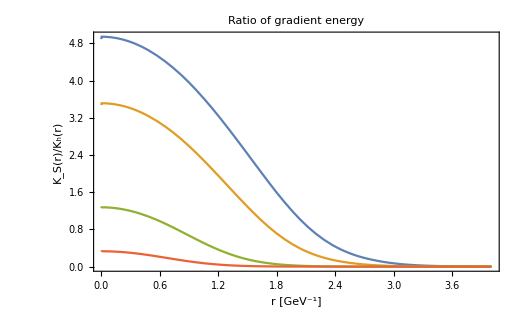

```mathematica
Plot[{KinS1[r]/Kinh1[r],KinS2[r]/Kinh2[r],KinS3[r]/Kinh3[r],KinS4[r]/Kinh4[r]},{r,0,4},BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["r [GeV^-1]",FontFamily->"Times",FontSize->18],Style["K_S(r)/K_h(r)",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotLabel->Style["Ratio of gradient energy"],Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4]},{Style["m_S = 1.67 GeV",FontFamily->"Times",FontSize->16],Style["m_S = 2.0 GeV",FontFamily->"Times",FontSize->16],Style["m_S = 3.76 GeV",FontFamily->"Times",FontSize->16],Style["m_S = 6.25 GeV",FontFamily->"Times",FontSize->16]}]}],RoundingRadius->5],Scaled[{0.82,0.75}]]},ImageSize->520]
```